```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
(*******************************)
```

```mathematica
dateMouseSessionListV1toV2m={{"091520","Mouse21060","Session1"},{"121420","Mouse23379","Session1"},{"101920","Mouse23392","Session1"},{"102620","Mouse23392","Session2"},{"020521","Mouse23320","Session2"},{"030121","Mouse23329","Session2"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"120120","Mouse23377","Session2"},{"113020","Mouse23378","Session2"},{"120120","Mouse23378","Session2"},{"112920","Mouse23384","Session2"},{"113020","Mouse23384","Session2"},{"120120","Mouse23384","Session2"},{"102120","Mouse23394","Session2"},{"011921","Mouse23369","Session1"},{"011921","Mouse23339","Session1"},{"062922","Mouse23067","Session1"},{"062922","Mouse23075","Session2"},{"070822","Mouse23075","Session1"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092321","Mouse22422","Session2"},{"100521","Mouse22422","Session2"},{"081721","Mouse22437","Session1"},{"081921","Mouse22437","Session2"},{"100421","Mouse22472","Session1"},{"102121","Mouse22422","Session1"},{"101721","Mouse22436","Session2"},{"071222","Mouse23025","Session1"},{"071122","Mouse23100","Session1"},{"070822","Mouse23014","Session2"},{"071522","Mouse23014","Session1"},{"070722","Mouse22518","Session2"},{"071322","Mouse22518","Session1"}};
```

```mathematica
(***************)
```

```mathematica
suppIndexValsV1toV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/V1toV2m/ValuesForPlotting/suppressionIndices_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
suppIndexValsLPtoV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LPtoV2m/ValuesForPlotting/suppressionIndices_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
suppIndexValsLMtoV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/Axons/LMtoV2m/ValuesForPlotting/suppressionIndices_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[suppIndexValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[suppIndexValsV1toV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[suppIndexValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[suppIndexValsLMtoV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[suppIndexValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[suppIndexValsLPtoV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[suppIndexValsLPtoV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Transparent,Frame->False],DistributionChart[suppIndexValsLPtoV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

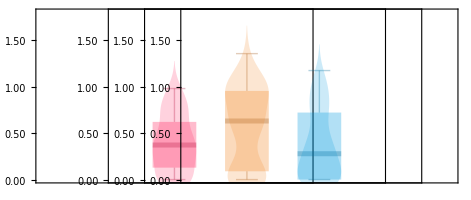

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,transp},Spacings->{{-280,-280,-280,-400}}]
```